## Frobenius expansions

```mathematica
ffrob[x_]:=(2x(1+s)-x^2(3+s)-4 I M ω)/(x^2(1-x));
gfrob[x_]:=-(4I M ω s/(x^2(1-x)^2)+(λ+x(1+s))/(x^2(1-x)))
```

```mathematica
ffrobCoeff[n_]:=SeriesCoefficient[(x-1)ffrob[x],{x,1,n}]
gfrobCoeff[n_]:=SeriesCoefficient[(x-1)^2gfrob[x],{x,1,n}]
```

```mathematica
Qα[α_]:=α(α-1)+ffrobCoeff[0]α+gfrobCoeff[0];
αSol=α/.Solve[Qα[α]==0,α]
```

{s,-4 ⅈ M ω}

```mathematica
Qα[α]
```

(-1+α) α-4 ⅈ M s ω+α (1-s+4 ⅈ M ω)

```mathematica
Clear[hypcoeff];
hypcoeff[0,j_]:=1;
hypcoeff[n_/;n>0,j_]:=hypcoeff[n,j]=Simplify[-Sum[((αSol[[j]]+k)ffrobCoeff[n-k]+gfrobCoeff[n-k])hypcoeff[k,j],{k,0,n-1}]/Qα[αSol[[j]]+n]]
```

```mathematica
Series[hypcoeff[1,1],{ω,0,2}]//FullSimplify
Series[hypcoeff[1,2],{ω,0,2}]//FullSimplify
```

(-1-2 s-λ/(1+s))+(4 ⅈ M (1+s (3+2 s)+λ) ω)/(1+s)^2+(16 M^2 (1+s (3+2 s)+λ) ω^2)/(1+s)^3+O[ω]^3

(1+s+λ)/(-1+s)-(4 ⅈ M (-1+3 s+λ) ω)/(-1+s)^2-(16 (M^2 (1+s (-1+2 s)+λ)) ω^2)/(-1+s)^3+O[ω]^3

```mathematica
With[{sval=2,lval=12,oval=0.11},
Clear[hypcoeffval];
hypcoeffval[0,j_]:=1;
hypcoeffval[n_/;n>0,j_]:=hypcoeffval[n,j]=Simplify[-Sum[((αSol[[j]]+k)ffrobCoeff[n-k]+gfrobCoeff[n-k])hypcoeffval[k,j],{k,0,n-1}]/Qα[αSol[[j]]+n]]/.λ->l(l+1)-s(s+1)/.s->sval/.l->lval/.ω->oval/.M->1
];
```

```mathematica
With[{NN=100,type=1},1-Sum[hypcoeffval[n,type](σ-1)^n/.σ->0.45,{n,0,NN}]/Sum[hypcoeffval[n,type](σ-1)^n/.σ->0.45,{n,0,NN-1}]]
```

1.57652×10^-14+1.78024×10^-13 ⅈ

```mathematica
(σ-1)^2Sum[hypcoeffval[n,1](σ-1)^n,{n,0,100}]/.σ->0.45`40
(σ-1)^(-4I (0.11`600))Sum[hypcoeffval[n,2](σ-1)^n,{n,0,100}]/.σ->0.45`40
```

3.96331×10^7-8.07586×10^7 ⅈ

3.81549×10^12-7.03829×10^12 ⅈ

```mathematica
(A(σ-1)^(-4I (0.11))Sum[hypcoeffval[n,2](σ-1)^n,{n,0,50}]+B(σ-1)^2Sum[hypcoeffval[n,1](σ-1)^n,{n,0,50}])/.σ->0.6/.B->2.1905310^75-3.910210^74 I/.A->4.8197710^75-1.9753510^77 I
```

-1.53227×10^53-2.47022×10^53 ⅈ

```mathematica
With[{sval=2,lval=12,oval=0.11,x=0.8},{D[(σ-1)^(-4I (0.11))Sum[hypcoeffval[n,2](σ-1)^n,{n,0,50}],{σ,2}],ffrob[σ]D[(σ-1)^(-4I (0.11))Sum[hypcoeffval[n,2](σ-1)^n,{n,0,50}],{σ,1}]+gfrob[σ]D[(σ-1)^(-4I (0.11))Sum[hypcoeffval[n,2](σ-1)^n,{n,0,50}],{σ,0}]/.λ->l(l+1)-s(s+1)/.s->sval/.l->lval/.ω->oval/.M->1}/.σ->x
]
```

{9.03392×10^9-5.96471×10^9 ⅈ,-9.03392×10^9+5.96471×10^9 ⅈ}

```mathematica
With[{sval=2,lval=12,oval=0.11,x=0.8},{D[(σ-1)^2Sum[hypcoeffval[n,1](σ-1)^n,{n,0,50}],{σ,2}],ffrob[σ]D[(σ-1)^2Sum[hypcoeffval[n,1](σ-1)^n,{n,0,50}],{σ,1}]+gfrob[σ]D[(σ-1)^2Sum[hypcoeffval[n,1](σ-1)^n,{n,0,50}],{σ,0}]/.λ->l(l+1)-s(s+1)/.s->sval/.l->lval/.ω->oval/.M->1}/.σ->x
]
```

{98711.1-71081.2 ⅈ,-98711.1+71081.2 ⅈ}

```mathematica
With[{sval=2,lval=12,oval=0.11,x=0.9},{D[(σ-1)^2Sum[hypcoeffval[n,1](σ-1)^n,{n,0,50}],{σ,1}](σ-1)^(-4I (0.11))Sum[hypcoeffval[n,2](σ-1)^n,{n,0,50}],(σ-1)^2Sum[hypcoeffval[n,1](σ-1)^n,{n,0,50}]D[(σ-1)^(-4I (0.11))Sum[hypcoeffval[n,2](σ-1)^n,{n,0,50}],{σ,1}]}/.σ->x
]
```

{-1.45817×10^6+1.31819×10^6 ⅈ,-1.45817×10^6+1.31819×10^6 ⅈ}

```mathematica
With[{sval=2,lval=12,oval=0.11,x=0.8},{ffrob[σ],gfrob[σ]}/.λ->l(l+1)-s(s+1)/.s->sval/.l->lval/.ω->oval/.M->1/.σ->x
]
```

{12.5-3.4375 ⅈ,-1190.63-34.375 ⅈ}

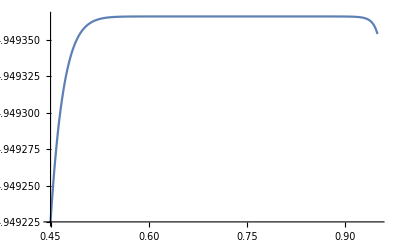

```mathematica
Plot[{RealExponent[(σ-1)^(-4I (0.11))Sum[hypcoeffval[n,2](σ-1)^n,{n,0,50}]/((σ-1)^(2)Sum[hypcoeffval[n,1](σ-1)^n,{n,0,50}])]},{σ,0.45,0.95},PlotRange->All]
```

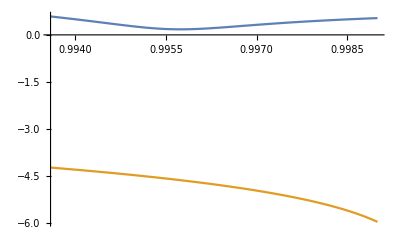

```mathematica
Plot[{RealExponent[(σ-1)^(-4I (0.11))Sum[hypcoeffval[n,2](σ-1)^n,{n,0,50}]],RealExponent[(σ-1)^(2)Sum[hypcoeffval[n,1](σ-1)^n,{n,0,50}]]},{σ,1-1/(12 13),0.999}]
```

## Asymptotic expansions

```mathematica
Series[ffrob[x],{x,0,2}]
Series[gfrob[x],{x,0,2}]
```

-(4 ⅈ M ω)/x^2+(2 (1+s-2 ⅈ M ω))/x+(-1+s-4 ⅈ M ω)+(-1+s-4 ⅈ M ω) x+(-1+s-4 ⅈ M ω) x^2+O[x]^3

(-λ-4 ⅈ M s ω)/x^2+(-1-s-λ-8 ⅈ M s ω)/x+(-1-s-λ-12 ⅈ M s ω)+(-1-s-λ-16 ⅈ M s ω) x+(-1-s-λ-20 ⅈ M s ω) x^2+O[x]^3

```mathematica
Series[D[Exp[Sum[A[n]x^n,{n,-2,-1}]],{x,2}]/Exp[Sum[A[n]x^n,{n,-2,-1}]],{x,0,3}]//FullSimplify
```

(4 A[-2]^2)/x^6+(4 A[-2] A[-1])/x^5+(6 A[-2]+A[-1]^2)/x^4+(2 A[-1])/x^3+O[x]^4

```mathematica
Series[gfrob[x],{x,0,1}]
```

(-λ-4 ⅈ M s ω)/x^2+(-1-s-λ-8 ⅈ M s ω)/x+(-1-s-λ-12 ⅈ M s ω)+(-1-s-λ-16 ⅈ M s ω) x+O[x]^2

```mathematica
solPre[x_]:=Exp[Sum[A[n]x^n,{n,-1,-1}]+A[L]Log[x]];
solTemp[x_]:=solPre[x](1+Sum[B[n]x^n,{n,1,4}]);
```

```mathematica
D[solTemp[x],{x,2}]/solPre[x]//FullSimplify
```

2 B[2]+6 x B[3]+12 x^2 B[4]+(2 (-A[-1]+x A[L]) (B[1]+x (2 B[2]+x (3 B[3]+4 x B[4]))))/x^2+((A[-1] (2 x+A[-1])+x A[L] (-x-2 A[-1]+x A[L])) (1+x (B[1]+x (B[2]+x (B[3]+x B[4])))))/x^4

```mathematica
Series[FullSimplify[D[solTemp[x],{x,2}]/solPre[x]],{x,0,0}]+
Series[FullSimplify[ffrob[x]D[solTemp[x],{x,1}]/solPre[x]],{x,0,0}]/.A[-1]->0/.A[L]->0
```

-(4 ⅈ M ω B[1])/x^2+((2 (1+s)-4 ⅈ M ω) B[1]-8 ⅈ M ω B[2])/x+((-3-s+2 (1+s)-4 ⅈ M ω) B[1]+2 B[2]+2 (2 (1+s)-4 ⅈ M ω) B[2]-12 ⅈ M ω B[3])+O[x]^1

```mathematica
Series[FullSimplify[D[solTemp[x],{x,2}]/solPre[x]],{x,0,0}]+
Series[FullSimplify[ffrob[x]D[solTemp[x],{x,1}]/solPre[x]],{x,0,0}]/.A[-1]->0/.A[L]->0//FullSimplify
```

-(4 ⅈ M ω B[1])/x^2+(2 (1+s-2 ⅈ M ω) B[1]-8 ⅈ M ω B[2])/x+((-1+s-4 ⅈ M ω) B[1]+(6+4 s-8 ⅈ M ω) B[2]-12 ⅈ M ω B[3])+O[x]^1

```mathematica
Series[FullSimplify[D[solTemp[x],{x,2}]/solTemp[x]],{x,0,-2}]+
Series[FullSimplify[ffrob[x]D[solTemp[x],{x,1}]/solTemp[x]],{x,0,0}]/.A[-2]->0/.A[-1]->-4I M ω//FullSimplify
```

(4 M ω (2 ⅈ s+4 M ω+ⅈ A[L]))/x^3+((1+2 s-4 ⅈ M ω) A[L]+A[L]^2+4 ⅈ M ω (-1+s-4 ⅈ M ω+B[1]))/x^2+1/O[x]

```mathematica
Solve[4 M ω (2 ⅈ s+4 M ω+ⅈ A[L])==0,A[L]]
```

{{A[L]→-2 s+4 ⅈ M ω}}

```mathematica
FullSimplify[(1+x B[1])D[solTemp[x],{x,2}]/solTemp[x]]
```

1/x^6(4 A[-2]^2+x^4 A[L]^2 (1+x B[1])+4 x A[-2] (A[-1]+A[-2] B[1])+x^2 A[L] (-4 A[-2]-x (x+2 A[-1])+x (x^2-4 A[-2]-2 x A[-1]) B[1])+x^3 (2 A[-1]+(2 A[-2]+A[-1]^2) B[1])+x^2 (A[-1]^2+A[-2] (6+4 A[-1] B[1])))

```mathematica
FullSimplify[ffrob[x](1+x B[1])D[solTemp[x],{x,1}]/solTemp[x]]
```

1/((-1+x) x^5)(-2 (1+s) x+(3+s) x^2+4 ⅈ M ω) (x^3 B[1]-2 A[-2] (1+x B[1])-x A[-1] (1+x B[1])+x^2 A[L] (1+x B[1]))

```mathematica
Series[(1+x B[1])(FullSimplify[D[solTemp[x],{x,2}]/solTemp[x]]+
FullSimplify[ffrob[x]D[solTemp[x],{x,1}]/solTemp[x]]),{x,0,-3}]/.A[-2]->0/.A[-1]->0//FullSimplify
```

-(4 ⅈ M ω A[L])/x^3+1/O[x]^2

```mathematica
Series[(1+x B[1])(FullSimplify[D[solTemp[x],{x,2}]/solTemp[x]]+
FullSimplify[ffrob[x]D[solTemp[x],{x,1}]/solTemp[x]]),{x,0,-2}]/.A[-2]->0/.A[-1]->-4I M ω/.A[L]->-2 s+4 ⅈ M ω//FullSimplify
```

(s (-2+4 ⅈ M ω)+4 M ω (4 M ω+ⅈ B[1]))/x^2+1/O[x]

```mathematica
Solve[-(-λ-4 ⅈ M s ω)==s (-2+4 ⅈ M ω)+4 M ω (4 M ω+ⅈ B[1]),B[1]]
```

{{B[1]→(ⅈ (-2 s-λ+16 M^2 ω^2))/(4 M ω)}}

```mathematica
Series[(1+x B[1])(FullSimplify[D[solTemp[x],{x,2}]/solTemp[x]]),{x,0,2}]/.A[-2]->0/.A[-1]->0/.A[L]->0
```

O[x]^3

```mathematica
Series[(1+x B[1])(FullSimplify[D[solTemp[x],{x,2}]/solTemp[x]]+
FullSimplify[ffrob[x]D[solTemp[x],{x,1}]/solTemp[x]]),{x,0,-1}]+Series[gfrob[x],{x,0,1}]/.A[-2]->0/.A[-1]->0/.A[L]->0/.B[1]->(ⅈ λ-4 M s ω)/(4 M ω)//FullSimplify
```

(-1-2 s^2+(ⅈ (1+s) λ)/(2 M ω)-s (3+4 ⅈ M ω)-8 ⅈ M ω B[2])/x+O[x]^0

```mathematica
Solve[-(-λ-4 ⅈ M s ω)==-4 ⅈ M ω B[1],B[1]]/.λ->l(l+1)-s(s+1)/.s->2/.l->2/.ω->0.6/.M->1
```

{{B[1]→-2}}

```mathematica
Solve[-1-2 s^2+(ⅈ (1+s) λ)/(2 M ω)-s (3+4 ⅈ M ω)-8 ⅈ M ω B[2]==0,B[2]]
```

{{B[2]→(λ+s λ-8 M^2 s ω^2+2 ⅈ (M ω+3 M s ω+2 M s^2 ω))/(16 M^2 ω^2)}}

```mathematica
Series[(λ+s λ-8 M^2 s ω^2+2 ⅈ (M ω+3 M s ω+2 M s^2 ω))/(16 M^2 ω^2),{ω,0,4}]
```

(λ+s λ)/(16 M^2 ω^2)+(ⅈ (1+3 s+2 s^2))/(8 M ω)-s/2+O[ω]^5

```mathematica
(λ+s λ)/(16 M^2 ω^2)u^2/(I λ u/(4 M ω))//FullSimplify
```

-(ⅈ (1+s) u)/(4 M ω)

```mathematica
Series[(1+x B[1])(FullSimplify[D[solTemp[x],{x,2}]/solTemp[x]]+
FullSimplify[ffrob[x]D[solTemp[x],{x,1}]/solTemp[x]]),{x,0,0}]+Series[gfrob[x],{x,0,1}]/.A[-2]->0/.A[-1]->0/.A[L]->0/.B[1]->(ⅈ λ-4 M s ω)/(4 M ω)/.B[2]->(λ+s λ-8 M^2 s ω^2+2 ⅈ (M ω+3 M s ω+2 M s^2 ω))/(16 M^2 ω^2)//FullSimplify
```

1/(16 M^2 ω^2)(-((1+s) λ^2)+2 λ (3+5 s+2 s^2-ⅈ M (7+s (7+4 s)) ω+4 M^2 s ω^2)+4 ⅈ M ω (3+s (11+12 s+4 s^2-2 ⅈ M (1+s+2 s^2) ω+8 M^2 (-2+s) ω^2)-48 M^2 ω^2 B[3]))+O[x]^1

```mathematica
Solve[1/(16 M^2 ω^2)(-((1+s) λ^2)+2 λ (3+5 s+2 s^2-ⅈ M (7+s (7+4 s)) ω+4 M^2 s ω^2)+4 ⅈ M ω (3+s (11+12 s+4 s^2-2 ⅈ M (1+s+2 s^2) ω+8 M^2 (-2+s) ω^2)-48 M^2 ω^2 B[3]))==0,B[3]]/.λ->0/.s->0//FullSimplify
```

{{B[3]→1/(16 M^2 ω^2)}}

## Teukolsky

```mathematica
Kv[r_]:=(r^2+a^2)ω-m a;
Δ[r_]:=r^2-2M r + a^2;
```

```mathematica
teukF[r_]:=(2(r-M)(1+s)/Δ[r])/.{om->ω,a->q,M->1};
teukV[r_]:=((Kv[r]^2-2I s(r-M)Kv[r])/Δ[r]^2+(4I s ω r-λ)/Δ[r])/.{om->ω,a->q,M->1};
```

```mathematica
Series[teukF[r],{r,Infinity,2}]
Series[teukV[r],{r,Infinity,2}]
```

(2 (1+s))/r+(2 (1+s))/r^2+O[1/r]^3

ω^2+(2 ⅈ s ω+4 ω^2)/r+(-λ-2 m q ω+2 ⅈ s ω+12 ω^2)/r^2+O[1/r]^3

```mathematica
λsolTeuk=Solve[λ^2+SeriesCoefficient[teukF[r],{r,Infinity,0}]λ+SeriesCoefficient[teukV[r],{r,Infinity,0}]==0,λ];
μsolTeuk=-(SeriesCoefficient[teukF[r],{r,Infinity,1}]λ+SeriesCoefficient[teukV[r],{r,Infinity,1}])/(SeriesCoefficient[teukF[r],{r,Infinity,0}]+2λ)/.λsolTeuk//Simplify;
normTeuk=(SeriesCoefficient[teukF[r],{r,Infinity,0}]+2λ)/.λsolTeuk;
λsolTeuk=λ/.λsolTeuk;
```

```mathematica
coeffTeuk[0,j_]:=1
coeffTeuk[n_/;n>0,j_]:=((n-μsolTeuk[[j]])(n-1-μsolTeuk[[j]])coeffTeuk[n-1,j]+Sum[(λsolTeuk[[j]]SeriesCoefficient[teukF[r],{r,Infinity,k+1}]+SeriesCoefficient[teukV[r],{r,Infinity,k+1}]-(n-k-μsolTeuk[[j]])SeriesCoefficient[teukF[r],{r,Infinity,k}])coeffTeuk[n-k,j],{k,1,n}])/n/normTeuk[[j]]
```

```mathematica
λsolTeuk
μsolTeuk
```

{-ⅈ ω,ⅈ ω}

{-1-2 ⅈ ω,-1-2 s+2 ⅈ ω}

```mathematica
coeffTeuk[1,1]/.q->0//FullSimplify
coeffTeuk[1,2]/.q->0//FullSimplify
```

2 s-(ⅈ (2 s+λ))/(2 ω)+4 ⅈ ω

(ⅈ (λ-8 ω^2))/(2 ω)

## Infinity expansion coefficients

```mathematica
Clear[aInf];
aInf[-1]=0;
aInf[0]=1;
aInf[n_/;n>0]:=aInf[n]=Simplify[-(AInf[n-1]aInf[n-2]+BInf[n-1]aInf[n-1])/CInf[n-1]];
AInf[n_]:=-(αCH +(n-1)ϵCH)(αCH-γCH ϵCH +n ϵCH);
BInf[n_]:=αCH^2+αCH(ϵCH(-γCH-δCH+2n+1)+ϵCH^2)+ϵCH^2(n(-γCH-δCH+n+ϵCH+1)-qCH);
CInf[n_]:=-(n+1)ϵCH^3;
```

```mathematica
Clear[αCH,ϵCH,γCH,δCH,qCH];
```

```mathematica
ABRule={a->-s-I(2 ω-(2ω - m q)/κ)/2,b->I(2 ω+(2ω - m q)/κ)/2};
αCHRule=(4I ω κ)(1+2s-2I ω +a+b)/.ABRule;
γCHRule=s+1+2a/.ABRule;
δCHRule =s+1+2b/.ABRule;
ϵCHRule=4I ω κ;
qCHRule=-(b+a)(s+1)-2a b +λ-(2ω)^2/2+(2 ω-m q)^2/κ^2/2+2 ω m q -2 ω(2 ω+I s)(1-κ)+2I ω s κ + 2I ω κ(1+2a)/.ABRule;
```

```mathematica
CHRule={αCH->αCHRule,γCH->γCHRule, δCH->δCHRule, ϵCH->ϵCHRule,qCH->qCHRule};
κRule={κ->Sqrt[1-q^2]};
```

## Horizon expansion coefficients

```mathematica
Clear[aHor];
aHor[-1]=0;
aHor[0]=1;
aHor[n_/;n>0]:=aHor[n]=Simplify[-(AHor[n-1]aHor[n-2]+BHor[n-1]aHor[n-1])/CHor[n-1]];
AHor[n_]:=αCH+ϵCH(n-δCH);
BHor[n_]:=n^2+n(γCH-δCH+ϵCH+1)+(1-δCH)(γCH+ϵCH)-qCH+αCH;
CHor[n_]:=(n-δCH+2)(n+1);
```

```mathematica
Clear[αCH,ϵCH,γCH,δCH,qCH];
```

```mathematica
ABRule={a->-s-I(2 ω-(2ω - m q)/κ)/2,b->I(2 ω+(2ω - m q)/κ)/2};
αCHRule=(4I ω κ)(1+2s-2I ω +a+b)/.ABRule;
γCHRule=s+1+2a/.ABRule;
δCHRule =s+1+2b/.ABRule;
ϵCHRule=4I ω κ;
qCHRule=-(b+a)(s+1)-2a b +λ-(2ω)^2/2+(2 ω-m q)^2/κ^2/2+2 ω m q -2 ω(2 ω+I s)(1-κ)+2I ω s κ + 2I ω κ(1+2a)/.ABRule;
```

```mathematica
CHRule={αCH->αCHRule,γCH->γCHRule, δCH->δCHRule, ϵCH->ϵCHRule,qCH->qCHRule};
κRule={κ->Sqrt[1-q^2]};
```

```mathematica
aHor[0]/.CHRule/.κ->1/.q->0//FullSimplify
aHor[1]/.CHRule/.q->0/.κ->1//FullSimplify
aHor[2]/.CHRule/.q->0/.κ->1//FullSimplify
```

1

(-λ+s (-2+4 ⅈ ω)+16 ω^2)/(-1+s+4 ⅈ ω)

(-4 s+8 s^2-2 λ+6 s λ+λ^2-4 ⅈ (1+s (-3+6 s+2 λ)) ω-16 (s (5+s)+2 λ) ω^2+64 ⅈ (1+2 s) ω^3+256 ω^4)/(2 (-2+s+4 ⅈ ω) (-1+s+4 ⅈ ω))

```mathematica
(-λ+s (-2+4 ⅈ ω)+16 ω^2)/(-1+s+4 ⅈ ω)((-λ+s (-2+4 ⅈ ω)+16 ω^2)/(-1+s+4 ⅈ ω)/.Complex[X_,Y_]:>Complex[X,-Y])//FullSimplify//Apart//FullSimplify
```

((2 s+λ)^2+16 ((-4+s) s-2 λ) ω^2+256 ω^4)/((-1+s)^2+16 ω^2)

```mathematica
Solve[A/B(1-σ)/(2 ω σ)==1,σ]//FullSimplify
```

{{σ→A/(A+2 B ω)}}